Radiation pressure for degenerate internal squeezing
Using radiation pressure term from Hamiltonian in Li et al, 2020

```mathematica
(*unifying symbols: SRC mode is now b, losses are now γ*)
(*changing ωs to ⅈ ωs in Hamiltonian, ϕ=π/2 preserves sign of χ for squeezing*)
(*setting global assumptions*)
$Assumptions={Ω≥0,γa≥0,γbtot≥γR>0,1>Rpd≥0,χ≥0,ωs>0,Element[β,Reals],ρRP≥0,Element[ϕ,Reals]};
(*β=(αGW Larm)/(2^(1/2)ℏ), ρRP=αGW^2/(2^(1/2)ℏ μ);*)

Id=IdentityMatrix[2];
(*simplifying upstream to better the end result*)
Ma=(γa-ⅈ Ω)Id+(ⅈ ρRP)/(2^(1/2)Ω^2)({{1, 1}, {-1, -1}});
invMa=Inverse[Ma]//Simplify;
Mb=(γbtot-ⅈ Ω)Id+ωs^2 invMa+χ({{0, ⅈ Exp[ⅈ ϕ]}, {-ⅈ Exp[-ⅈ ϕ], 0}});(*ϕ free in Hamiltonian, recover when ϕ=π/2*)
invMb=Inverse[Mb]//Simplify;

Γ=1/2^(1/2)({{1, 1}, {-ⅈ, ⅈ}});
Rin=((1-Rpd)^(1/2)Γ.(Id-2 γR invMb).Inverse[Γ])//Simplify;
Ra=(-(1-Rpd)^(1/2)2 ωs(γR γa)^(1/2)Γ. invMb.invMa.Inverse[Γ])//Simplify;(*ωs to ⅈ ωs in Hamiltonian*)
Rb=(-(1-Rpd)^(1/2)2( γR(γbtot-γR))^(1/2)Γ. invMb.Inverse[Γ])//Simplify;
T=(-(1-Rpd)^(1/2)ωs (-ⅈ β)(2 γR)^(1/2)Γ. invMb.invMa.({{1, 0}, {0, -1}}))//Simplify;(*ωs to ⅈ ωs in Hamiltonian*)

FlipI={ⅈ->-ⅈ,Complex[RePart_,ImPart_]->Complex[RePart,-ImPart]};
ConjugateFlipI=Conjugate[f_]:>(f/.FlipI);
Sx=Simplify[(
Rin.ConjugateTranspose[Rin]
+Ra.ConjugateTranspose[Ra]
+Rb.ConjugateTranspose[Rb]
+Rpd Id)/.ConjugateFlipI,TimeConstraint->{1,5}];
(*signal transfer function is Subscript[X, PD,2] wrt h not (X⃗)_PD wrt h⃗*)
sigTransfer = Simplify[(T.({{1}, {1}}))[[2]][[1]],TimeConstraint->{1,5}];(*2nd index: [[1]] to remove atomic brackets {...}*)
sigTransferAbs=ComplexExpand[Abs[sigTransfer]]//Simplify;
Sh=Simplify[Sx[[2,2]]/sigTransferAbs^2,TimeConstraint->{1,5}];
```

Simplify::gtime: Returning the simplest form found in the allowed time of 5. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::gtime: Returning the simplest form found in the allowed time of 5. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

```mathematica
(*signal transfer function -- demonstration of factor of two*)
FullSimplify[(T.({{1}, {1}}))[[2]][[1]]/.{ρRP->0,Rpd->0,γa->0,γbtot->γR,β->-β,ϕ->π/2}];
FullSimplify[(T.ConjugateTranspose[T])[[2,2]]/.{ρRP->0,Rpd->0,γa->0,γbtot->γR,β->-β,ϕ->π/2}];
Print["sig. transfer fn.: ",Simplify[ComplexExpand[Abs[%%]^2]]," vs ", %]
```

sig. transfer fn.: (4 β^2 γR ωs^2)/((γR+χ)^2 Ω^2+(Ω^2-ωs^2)^2) vs (2 β^2 γR ωs^2)/((γR+χ)^2 Ω^2+Ω^4-2 Ω^2 ωs^2+ωs^4)

```mathematica
(*with RP off, does it reduce to (ASD)^2 from degIntSqz.nb?*)
PSDShdegIntSqz=1/(4 γR ωs^2 β^2)((((2γR-γbtot-χ)γa+Ω^2-ωs^2)^2
						+Ω^2(γa-(2γR-γbtot-χ))^2)
+(γa^2+ Ω^2)4γR (γbtot-γR)
+4γR γa ωs^2
+ Rpd/(1-Rpd)(((-γbtot-χ)γa+Ω^2-ωs^2)^2
		+Ω^2(γa-(-γbtot-χ))^2));
Print["Rad. pressure off, does Sh reduce to degIntSqz?: ",(%==(Sh/.{ρRP->0,β->-β,ϕ->π/2}))//ComplexExpand//Simplify]
```

Rad. pressure off, does Sh reduce to degIntSqz?: True

```mathematica
Collect[ComplexExpand[Sx[[2,2]]/.ϕ->π/2],{ρRP},FullSimplify]
```

((γa^2+Ω^2) (γbtot^2+2 γbtot χ+4 (-1+Rpd) γR χ+χ^2+Ω^2)+2 (γa (γbtot+χ)-Ω^2) ωs^2+ωs^4)/((γa^2+Ω^2) ((γbtot+χ)^2+Ω^2)+2 (γa (γbtot+χ)-Ω^2) ωs^2+ωs^4)-(8 (-1+Rpd) γR ρRP^2 ωs^2 (γa ((γbtot-χ)^2+Ω^2)+γbtot ωs^2))/(Ω^4 ((γa^2+Ω^2) ((γbtot+χ)^2+Ω^2)+2 (γa (γbtot+χ)-Ω^2) ωs^2+ωs^4) ((γa^2+Ω^2) ((γbtot-χ)^2+Ω^2)-2 (γa (-γbtot+χ)+Ω^2) ωs^2+ωs^4))

```mathematica
(*stability is not the same: recognise denominator as the same as degIntSqz or the same * samewithχflip, therefore pole-defined threshold values are the same with the addition of the χflip values as well*)
((γbtot^2 Ω^2+2 γbtot χ Ω^2+χ^2 Ω^2+Ω^4+γa^2 (γbtot^2+2 γbtot χ+χ^2+Ω^2)+2 γa (γbtot+χ) ωs^2-2 Ω^2 ωs^2+ωs^4)==Abs[(γbtot+χ-I Ω)(γa-ⅈ Ω)+ωs^2]^2)//ComplexExpand//Simplify
((γbtot^4 Ω^4+γa^4 (γbtot^4-2 γbtot^2 (χ^2-Ω^2)+(χ^2+Ω^2)^2)+4 γa^3 γbtot (γbtot^2-χ^2+Ω^2) ωs^2+2 γbtot^2 Ω^2 (-χ^2 Ω^2+(Ω^2-ωs^2)^2)+4 γa γbtot ωs^2 (γbtot^2 Ω^2-χ^2 Ω^2+(Ω^2-ωs^2)^2)+(χ^2 Ω^2+(Ω^2-ωs^2)^2)^2+2 γa^2 (γbtot^4 Ω^2+χ^4 Ω^2+(Ω^3-Ω ωs^2)^2+χ^2 (2 Ω^4-2 Ω^2 ωs^2-ωs^4)+γbtot^2 (-2 χ^2 Ω^2+2 Ω^4-2 Ω^2 ωs^2+3 ωs^4)))==(Abs[(γbtot+χ-I Ω)(γa-ⅈ Ω)+ωs^2](Abs[(γbtot+χ-I Ω)(γa-ⅈ Ω)+ωs^2]/.χ->-χ))^2)//ComplexExpand//Simplify
```

True

True

```mathematica
(*simplify Sx22, from nIS_RP.nb*)
Block[{
noiseΔSx=Together[Sx[[2,2]]-1],
SimplifyConstrained=FullSimplify[#,TimeConstraint->{0.1,1}]&},
numerΔSx=Collect[Numerator[noiseΔSx],{ϕ,ρRP},SimplifyConstrained];
denomΔSx=Collect[Denominator[noiseΔSx],{ϕ,ρRP},SimplifyConstrained];]
commonFactor0=1/4 Exp[-2ⅈ ϕ];
numerΔSxSimpl=Collect[(commonFactor0 numerΔSx)//ExpToTrig,{ϕ,ρRP},FullSimplify];
denomΔSxSimpl=Collect[(commonFactor0 denomΔSx)//ExpToTrig,{ϕ,ρRP},FullSimplify];
(*denominator is not the same as no RP case if pump phase is not π/2*)
Print["S_X=1 + (",numerΔSxSimpl,")\n/\n(",denomΔSxSimpl,")"]
```

S_X=1 + (4 √2 (-1+Rpd) γR ρRP χ Ω^2 ωs^2 Cos[ϕ] (γa^2 γbtot-3 γbtot Ω^2+γa (-4 Ω^2+ωs^2)+χ (γa^2+Ω^2) Sin[ϕ])+4 (-1+Rpd) γR χ Ω^4 (γa^2+Ω^2) (-2 χ (γbtot (γa^2+Ω^2)+γa ωs^2)+((γa^2+Ω^2) (γbtot^2+χ^2+Ω^2)+2 (γa γbtot-Ω^2) ωs^2+ωs^4) Sin[ϕ])-4 (-1+Rpd) γR ρRP^2 ωs^2 (γa (2 γbtot^2+χ^2+2 Ω^2)+2 γbtot ωs^2-γa χ (χ Cos[2 ϕ]+4 γbtot Sin[ϕ])))
/
(Ω^4 ((γa^2+Ω^2) ((γbtot+χ)^2+Ω^2)+2 γa γbtot ωs^2+2 γa χ ωs^2-2 Ω^2 ωs^2+ωs^4) ((γa^2+Ω^2) ((γbtot-χ)^2+Ω^2)-2 (γa (-γbtot+χ)+Ω^2) ωs^2+ωs^4)+2 √2 ρRP χ Ω^2 ωs^2 (-γbtot^2 Ω^2+χ^2 Ω^2+Ω^4+γa^2 (γbtot^2-χ^2-Ω^2)-2 Ω^2 ωs^2+ωs^4+2 γa γbtot (-2 Ω^2+ωs^2)) Cos[ϕ]+2 ρRP^2 χ^2 ωs^4 Cos[ϕ]^2)

```mathematica
Block[{sigTsqr=Together[sigTransferAbs^2]},
SimplifyConstrained=FullSimplify[#,TimeConstraint->{0.1,1}]&;
commonFactor0=1/2;
numerTsqr=Collect[commonFactor0 Numerator[sigTsqr],{ϕ,ρRP},SimplifyConstrained];
denomTsqr=Collect[commonFactor0 Denominator[sigTsqr],{ϕ,ρRP},SimplifyConstrained];]
Print["(",numerTsqr,")\n/\n(",denomTsqr,")"]
```

(-2 (-1+Rpd) β^2 γR Ω^4 ωs^2 ((γa^2+Ω^2) (2 γbtot^2+χ^2+2 Ω^2)+4 (γa γbtot-Ω^2) ωs^2+2 ωs^4-χ^2 (γa^2+Ω^2) Cos[2 ϕ]-4 χ (γbtot (γa^2+Ω^2)+γa ωs^2) Sin[ϕ]))
/
(Ω^4 ((γa^2+Ω^2) ((γbtot+χ)^2+Ω^2)+2 (γa (γbtot+χ)-Ω^2) ωs^2+ωs^4) ((γa^2+Ω^2) ((γbtot-χ)^2+Ω^2)-2 (γa (-γbtot+χ)+Ω^2) ωs^2+ωs^4)+2 √2 ρRP χ Ω^2 ωs^2 (-γbtot^2 Ω^2+χ^2 Ω^2+Ω^4+γa^2 (γbtot^2-χ^2-Ω^2)-2 Ω^2 ωs^2+ωs^4+2 γa γbtot (-2 Ω^2+ωs^2)) Cos[ϕ]+2 ρRP^2 χ^2 ωs^4 Cos[ϕ]^2)

```mathematica
(*SX22===1+(((…)+(…)Sin[ϕ])+(…)ρRP Cos[ϕ]+((…)+(…)Cos[2ϕ]+(…)Sin[ϕ])ρRP^2)/((…)+(…)ρRP Cos[ϕ]+(…)(ρRP Cos[ϕ])^2);
T===((…)+(…)Cos[2ϕ]+(…)Sin[ϕ])/((…)+(…)ρRP Cos[ϕ]+(…)(ρRP Cos[ϕ])^2)*)
```

```mathematica
(*zeros of denominator of transfer functions*)
slowSol=Solve[(denomΔSxSimpl/.χ->-χ(*to enter anti-squeezed quadrature*))==0,{Ω,χ}];
Print[Length[slowSol]," solutions found"]
DumpSave[NotebookDirectory[]<>"dIS_RP_slowSol.mx",slowSol];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

11 solutions found

```mathematica
Simplify[slowSol[[4]]/.{ρRP->0,ϕ->π/2},TimeConstraint->{1,10}]
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

Simplify::gtime: Returning the simplest form found in the allowed time of 10. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

{χ→1/2 √(-(4 γa^4 γbtot^2)/(3 (γa^2+Ω^2)^2)+(4 γa^4 Ω^2)/(3 (γa^2+Ω^2)^2)-(8 γa^2 γbtot^2 Ω^2)/(3 (1)^2)+106)+1/2 √(-(2 γa^4 γbtot^2)/(3 (γa^2+Ω^2)^2)+(2 γa^4 Ω^2)/(3 (1)^2)-(4 γa^2 1 Ω^2)/(3 1^2)+94+1/1+1+(1)^(1/3)/(3 2^(1/3)))}
 |  |  |  |

```mathematica
DumpGet[NotebookDirectory[]<>"dIS_RP_slowSol.mx"]
```

```mathematica
(*minsol from nIS_threshold.nb --> to display on both quadrature plot*)
(*doing this all for no RP and fixed pump phase at π/2
to-do: convert to finding general RP and phase solutions (Solve is hanging, that's the problem)*)
Grad0={D[numerΔSxSimpl/denomΔSxSimpl/.{ρRP->0,ϕ->π/2},Ω],D[numerΔSxSimpl/denomΔSxSimpl/.{ρRP->0,ϕ->π/2},χ]}//Simplify;
GradSx0[Ω0_,χ0_]:=Grad0/.{Ω->Ω0,χ->χ0}

minSol=Solve[{GradSx0[Ω,χ]=={0,0},Ω≥0,χ≥0,γbtot≥γR>0,ωs>0,γa≥0,1>Rpd≥0},{Ω,χ}]//Simplify;
Print["Solve[..., {Ω,χ}] found "<>ToString[Length[minSol]]<>" solutions"]

χSqzMinThresh[γa0_,γbtot0_,Rpd0_]:=Min[Select[χ/.minSol/.{γa->γa0,γbtot->γbtot0,Rpd->Rpd0},Not[#===Undefined]&]]
```

Solve[..., {Ω,χ}] found 6 solutions

```mathematica
(*-----------------------------------------------------------------------------------------------------------------*)

(*
(*parameters from Korobko et al, 2019: benchmark 3rd generation detector*)
c=3. 10^8(*ms^-1*);
ℏ=1. 10^-34(*Js*);
Larm=20. 10^3(*m*);
Lsrc=56.(*m*);
Pcirc= 4. 10^6(*W*);
λ0=1550. 10^-9(*m*);
ω0=2π c/λ0;
Titm=0.07;
Tsrc=0.35;
ωs=c(Titm/(4 Lsrc Larm))^(1/2);
τRoundTripArm=(2 Larm)/c;
τRoundTripSRC=(2Lsrc)/c;
γR=-1/(2 τRoundTripSRC)Log[1-Tsrc];
*)

(*parameters for LIGO Voyager -- from Li et al, 2020*)
c=3. 10^8(*ms^-1*);
ℏ=1. 10^-34(*Js*);
Larm=4. 10^3(*m*);
Pcirc=3. 10^6(*W*);
λ0=2. 10^-6(*m*);
ω0=2π c/λ0;
γR=2π 500.(*Hz*);
ωs=10γR;
τRoundTripArm=(2 Larm)/c;
Tsrm=0.046; (*assuming LIGO Voyager's Subscript[T, SRM] was used for γR*)
τRoundTripSRC=-1/(2 γR)Log[1-Tsrm];
Print["inferred Lsrc (in m) = ",c/2 τRoundTripSRC]


Print["ωs/γR=",ωs/γR]
β=-((2Pcirc Larm ω0)/(ℏ c))^(1/2);(*rescaling of α by 1/(2^(1/2)ℏ) seems to be in Li?, chosen β s.t. turning R.P. off should match
β=(αGW Larm)/(2^(1/2)ℏ);
ρRP=αGW^2/(2^(1/2)ℏ μ)=(2^(1/2)ℏ β^2)/(Larm^2 μ); but |α|=|αGW Larm|*)
M=200.(*kg*);
μ=M/4;
ρ=(2^(1/2)ℏ β^2)/(Larm^2 μ);
```

inferred Lsrc (in m) = 1124.23

ωs/γR=10.

```mathematica
γaFn[Tla_]:=-1/(2 τRoundTripArm)Log[1-Tla]
γbtotFn[Tlb_]:=γR+-1/(2 τRoundTripSRC)Log[1-Tlb]
(*plotting sensitivity -- un-simplified Sh*)
(*taking real part to discard numerical error in tiny imaginary parts*)
QNwRP[Ω0_,χ0_,ϕ0_,Tla_,Tlb_,Rpd0_,ρRPTrue_:True]:=Re[Sqrt[Sx[[2,2]]]]/.{
Ω->Ω0,χ->χ0,ϕ->ϕ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0]}
sigwRP[Ω0_,χ0_,ϕ0_,Tla_,Tlb_,Rpd0_,ρRPTrue_:True]:=Re[sigTransferAbs]/.{
Ω->Ω0,χ->χ0,ϕ->ϕ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0]}
ASDShwRP[Ω0_,χ0_,ϕ0_,Tla_,Tlb_,Rpd0_,ρRPTrue_:True]:=Re[Sqrt[Sh]]/.{
Ω->Ω0,χ->χ0,ϕ->ϕ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0]}
```

```mathematica
legendStyler[vals0_]:=(
If[Length[vals0]==5,vals=Join[vals0,{True}],vals=vals0];
paddedStrings=Insert[StringPadRight[{ToString[N[vals[[1]]/γbtotFn[vals[[4]]]]],ToString[vals[[3]]],ToString[vals[[4]]],ToString[vals[[5]]]},4],StringPadRight[ToString[N[vals[[2]]/(2π)]],5],2];
(*<> is StringJoin*)
Style[StringForm["χ/γbtot=``, "<>ToString[If[Mod[vals[[2]]-π/2,π]==0,StringPadRight[ToString[StringForm["ϕ=``π/2",If[Mod[vals[[2]]-π/2,2π]==0,"+","-"]]],12],StringForm["ϕ/(2π)=``",
paddedStrings[[2]]]]]<>"; T_(l, a)=``, T_(l, b)=``, R_PD=``"
<>If[Not[vals[[6]]],"; no RP",""],
paddedStrings[[1]],
paddedStrings[[3]],
paddedStrings[[4]],
paddedStrings[[5]]],
FontFamily->"Monospace"])

plotwRP[valsList_,plotLabel_:None,plotStyle_:{},fmin_:1(*Hz*),fmax_:10^5(*Hz*)]:=(
p1=LogLinearPlot[Evaluate[Table[20Log10[QNwRP@@Join[{2π f},valsList[[i]]]],{i,1,Length[valsList]}]],
{f,fmin,fmax},ImageSize->350,PlotLegends->LineLegend[Table[legendStyler[valsList[[i]]],{i,1,Length[valsList]}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],
ImagePadding->{{100,10},{1,All}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{fmin,fmax},All},PlotStyle->plotStyle,Frame->True,FrameLabel->{{"quantum noise transfer function,\n|R| / dB (20log10)",},{,If[ToString[plotLabel]==ToString[None],"degenerate internal squeezing\nparameters of LIGO Voyager",plotLabel]}},
PerformanceGoal->"Speed"];
p2=LogLogPlot[Evaluate[Table[sigwRP@@Join[{2π f},valsList[[i]]],{i,1,Length[valsList]}]],
{f,fmin,fmax},ImageSize->350,PlotLegends->LineLegend[Table[legendStyler[valsList[[i]]],{i,1,Length[valsList]}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],ImagePadding->{{100,10},{1,1}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{fmin,fmax},All},PlotStyle->plotStyle,Frame->True,FrameLabel->{{"signal transfer function,\n|T| / [?] (log scale)",},{,}},
PerformanceGoal->"Speed"];
p3=LogLogPlot[Evaluate[Join[
Table[ASDShwRP@@Join[{2π f},valsList[[i]]],{i,1,Length[valsList]}],
{If[10^3<#<4 10^3,5 10^-25,Null]&[f]}]],
{f,fmin,fmax},ImageSize->350,ImagePadding->{{100,10},{50,1}},PlotLegends->LineLegend[Join[Table[legendStyler[valsList[[i]]],{i,1,Length[valsList]}],{"5×10^-25Hz^(-1/2) target for 1–4 kHz"}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],PlotStyle->({q0,r0}=If[plotStyle≠{},QuotientRemainder[Length[valsList],Length[plotStyle]],{0,Length[valsList]}];
Join[Flatten[Table[plotStyle,{i,1,q0}],1],Table[,{i,1,r0}],{Directive[Red,DotDashed]}]),PlotRange->{{fmin,fmax},All},Filling->{Length[valsList]+1->Bottom},Frame->True,FrameLabel->{{"strain sensitivity (NSR)\n/ Hz^(-1/2) (log scale)",},{"frequency, f=Ω/(2π) / Hz (log scale)",}},
PerformanceGoal->"Speed"];
Column[{p1,p2,p3},Spacings->0])
```

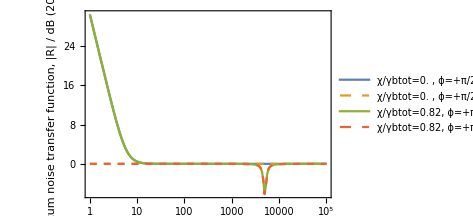
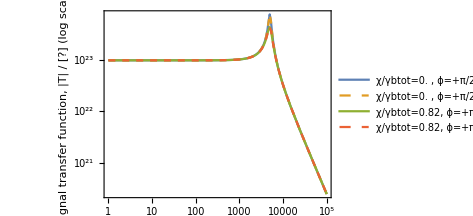
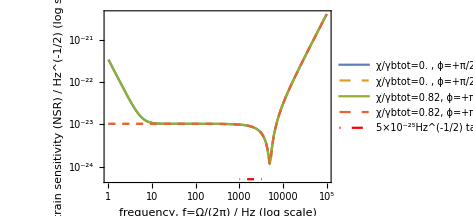

```mathematica
χRatio0=1;
loss0=0.01;
pumpPhase0=π/2;
valsList1={
{0,pumpPhase0,loss0,loss0,loss0},
{0,pumpPhase0,loss0,loss0,loss0,False},
{χRatio0 γR,pumpPhase0,loss0,loss0,loss0},
{χRatio0 γR,pumpPhase0,loss0,loss0,loss0,False}};
plotwRP[valsList1,None,{,Dashed}]
(*NB: we don't see change at LF -- like Korobko suggests*)
```

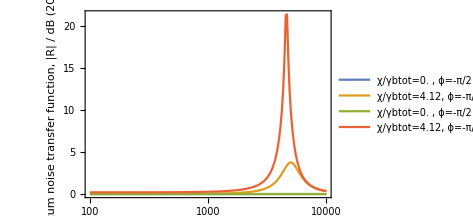
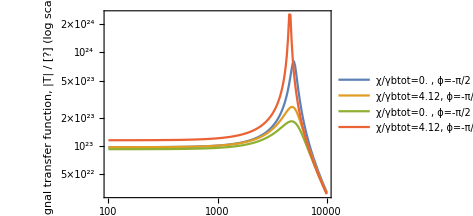
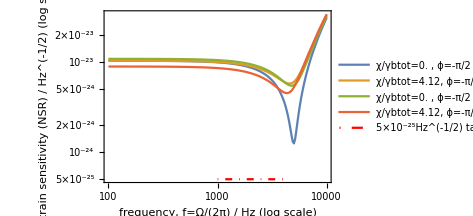

```mathematica
(*verifying that signal is amplified if pump phase is flipped*)
χRatio0=5;
loss0=0.01;
pumpPhase0=-π/2;
valsList1={
{0,pumpPhase0,0,loss0,loss0},
{χRatio0 γR,pumpPhase0,0,loss0,loss0},
{0,pumpPhase0,0.5,loss0,loss0},
{χRatio0 γR,pumpPhase0,0.5,loss0,loss0}};
plotwRP[valsList1,None,{},100,10^4]
(*limit of large arm loss not as useful because radiation pressure is not in DOPO model*)
(*here we can see that whether or not dIS improves sensitivity depends on the loss present and whether the decrease in noise outpaces the de-amplification of signal*)
```

```mathematica
(*NB: radiation pressure worsened because squeezing is in phase quadrature,
to-do: frequency dependent internal squeezing?*)
```

```mathematica
(*to-do: copy other plotting functions from degIntSqz:
NB: need to change parameters back to directly compare,
- stability --> changes, now becomes unstable on threshold -- why?,
- noise budget --> appears more vulnerable than nondegenerate case,
- optimum sensitivity at probe frequency --> linewidth is short so need to be close to ωs to see a difference,
*)
```

```mathematica
(*noise budget,
to-do: turn shot noise off to plot radiation pressure separately, how?*)
RpdwRP[Ω0_,χ0_,ϕ0_,Tla_,Tlb_,Rpd0_,ρRPTrue_:True]:=Re[Sqrt[(Rpd Id)[[2,2]]]]/.{
Ω->Ω0,χ->χ0,ϕ->ϕ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0]}
RinwRP[Ω0_,χ0_,ϕ0_,Tla_,Tlb_,Rpd0_,ρRPTrue_:True]:=Re[Sqrt[(Rin.ConjugateTranspose[Rin])[[2,2]]]]/.{
Ω->Ω0,χ->χ0,ϕ->ϕ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0]}
RawRP[Ω0_,χ0_,ϕ0_,Tla_,Tlb_,Rpd0_,ρRPTrue_:True]:=Re[Sqrt[(Ra.ConjugateTranspose[Ra])[[2,2]]]]/.{
Ω->Ω0,χ->χ0,ϕ->ϕ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0]}
RbwRP[Ω0_,χ0_,ϕ0_,Tla_,Tlb_,Rpd0_,ρRPTrue_:True]:=Re[Sqrt[(Rb.ConjugateTranspose[Rb])[[2,2]]]]/.{
Ω->Ω0,χ->χ0,ϕ->ϕ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0]}

plotNoiseBudgetwRP[params_,fRange_:{1,10^5}]:=
LogLinearPlot[{
20Log10[1],
20Log10[RinwRP@@Join[{2π f},params]],
20Log10[RawRP@@Join[{2π f},params]],
20Log10[RbwRP@@Join[{2π f},params]],
20Log10[RpdwRP@@Join[{2π f},params]],
20Log10[QNwRP@@Join[{2π f},params]]},{f,fRange[[1]],fRange[[2]]},PlotLegends->LineLegend[{"vacuum","R_in, behind SRM","(R^(L))_a, arm intra-cav.","(R^(L))_b, SRC signal intra-cav.","(R^(L))_PD, PD loss","total quantum noise"},LabelStyle->Directive[10],LegendLabel->legendStyler[params]],PlotRange->All,PlotStyle->{Directive[Gray,Dashed],,,,,Directive[Black,Dashed]},Frame->True,FrameLabel->{{"quantum noise transfer function,\n|R| / dB (20log10)",},{"frequency, f=Ω/(2π) / Hz","degenerate internal squeezing\nparameters of LIGO Voyager"}},PerformanceGoal->"Speed"]
```

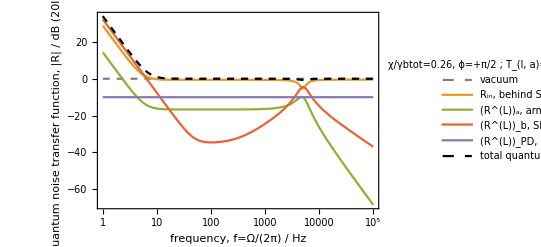

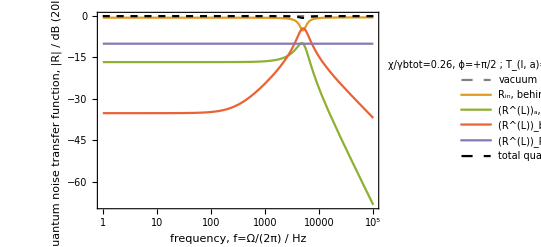

```mathematica
χRatio0=0.85;
plotNoiseBudgetwRP[{χRatio0 γR,π/2,0.1,0.1,0.1}]
plotNoiseBudgetwRP[{χRatio0 γR,π/2,0.1,0.1,0.1,False}]
```

```mathematica
(*optimum sensitivity at probe frequency, ϕ=π/2 is fixed,
to-do: allow ϕ freedom*)
plotThresholdFinder[fProbe_,pastThreshold_:False,ρRPTrue_:True]:=(
probeNoiseRef=QNwRP[2π fProbe,0,π/2,0,0,0,ρRPTrue];(*reference has no γc loss*)
probeSigRef=sigwRP[2π fProbe,0,π/2,0,0,0,ρRPTrue];
probeSensRef=ASDShwRP[2π fProbe,0,π/2,0,0,0,ρRPTrue];
rpdList=Subdivide[0,0.5,5];
p1=ParametricPlot[Evaluate[Flatten[Table[{
{-20Log10[QNwRP[2π fProbe,χRatio γR,π/2,0,0,rpdList[[i]],ρRPTrue]/probeNoiseRef],-20Log10[ASDShwRP[2π fProbe,χRatio γR,π/2,0,0,rpdList[[i]],ρRPTrue]/probeSensRef]}},{i,1,Length[rpdList]}],1]],{χRatio,0,1},Frame->True,FrameLabel->{{StringForm["SNR (Hz^(1/2)) gain at `` kHz\nrelative to no loss/sqz. / dB (20 log_10(1/S_h))",N[fProbe/10^3]],},{,"degenerate internal squeezing\nparameters of LIGO Voyager"}},PlotStyle->Table[Blend[{Blue,Green},(i-1)/Length[rpdList]],{i,1,Length[rpdList]}],PlotLegends->LineLegend[{Table[StringForm["χ/γR∈(0,1), R_PD=``",NumberForm[N[rpdList[[i]]]]],{i,1,Length[rpdList]}]},LabelStyle->Directive[10],LegendLabel->StringForm[If[Not[ρRPTrue],"no RP","with RP"],NumberForm[N[Tlc]]]],PlotRange->All,ImagePadding->{{80,10},{1,All}},ImageSize->350,AspectRatio->1,PerformanceGoal->"Speed"];
p2=ParametricPlot[{
{-20Log10[QNwRP[2π fProbe,1  γR,π/2,0,0,Rpd,ρRPTrue]/probeNoiseRef],-20Log10[ASDShwRP[2π fProbe,1  γR,π/2,0,0,Rpd,ρRPTrue]/probeSensRef]}},{Rpd,rpdList[[1]],rpdList[[-1]]},Frame->True,PlotStyle->Directive[Black,Dashed],PlotLegends->LineLegend[{StringForm["χ/γR=1, varying R_PD∈(``,``)",NumberForm[N[rpdList[[1]]]],NumberForm[N[rpdList[[-1]]]]]},LabelStyle->Directive[10]],PlotRange->All,ImagePadding->{{80,10},{1,All}},ImageSize->350,PerformanceGoal->"Speed"];
If[pastThreshold,
p1b=ParametricPlot[Evaluate[Flatten[Table[{
{-20Log10[QNwRP[2π fProbe,χRatio  γR,π/2,0,0,rpdList[[i]],ρRPTrue]/probeNoiseRef],-20Log10[ASDShwRP[2π fProbe,χRatio  γR,π/2,0,0,rpdList[[i]],ρRPTrue]/probeSensRef]}},{i,1,Length[rpdList]}],1]],{χRatio,1,2},Frame->True,PlotStyle->Table[Blend[{Red,Yellow},(i-1)/Length[rpdList]],{i,1,Length[rpdList]}],PlotLegends->LineLegend[{Table[StringForm["χ/γR∈(1,2), R_PD=``",NumberForm[N[rpdList[[i]]]]],{i,1,Length[rpdList]}]},LabelStyle->Directive[10]],PlotRange->All,ImagePadding->{{80,10},{1,All}},ImageSize->350,PerformanceGoal->"Speed"];
p1and2=Show[p1,p1b,p2];,
p1and2=Show[p1,p2];];
p3=ParametricPlot[Evaluate[Flatten[Table[{
{-20Log10[QNwRP[2π fProbe,χRatio  γR,π/2,0,0,rpdList[[i]],ρRPTrue]/probeNoiseRef],20Log10[sigwRP[2π fProbe,χRatio  γR,π/2,0,0,rpdList[[i]],ρRPTrue]/probeSigRef]}},{i,1,Length[rpdList]}],1]],{χRatio,0,1},Frame->True,FrameLabel->{{StringForm["signal transfer function |T| at `` kHz\nrelative to no loss/sqz. / dB (20 log_10)",N[fProbe/10^3]],},{StringForm["quantum noise transfer function |R| at `` kHz\nrelative to no loss/sqz. / dB (-20 log_10)",N[fProbe/10^3]],}},PlotStyle->Table[Blend[{Blue,Green},(i-1)/Length[rpdList]],{i,1,Length[rpdList]}],PlotRange->All,ImagePadding->{{80,10},{All,1}},ImageSize->350,AspectRatio->3/4,PerformanceGoal->"Speed"];
p4=ParametricPlot[
{-20Log10[QNwRP[2π fProbe,1  γR,π/2,0,0,Rpd,ρRPTrue]/probeNoiseRef],
20Log10[sigwRP[2π fProbe,1  γR,π/2,0,0,Rpd,ρRPTrue]/probeSigRef]},{Rpd,rpdList[[1]],rpdList[[-1]]},Frame->True,PlotStyle->Directive[Black,Dashed],PlotRange->All,ImagePadding->{{80,10},{All,1}}];
If[pastThreshold,
p3b=ParametricPlot[Evaluate[Flatten[Table[{
{-20Log10[QNwRP[2π fProbe,χRatio  γR,π/2,0,0,rpdList[[i]],ρRPTrue]/probeNoiseRef],20Log10[sigwRP[2π fProbe,χRatio  γR,π/2,0,0,rpdList[[i]],ρRPTrue]/probeSigRef]}},{i,1,Length[rpdList]}],1]],{χRatio,1,2},Frame->True,PlotStyle->Table[Blend[{Red,Yellow},(i-1)/Length[rpdList]],{i,1,Length[rpdList]}],PlotRange->All,ImagePadding->{{80,10},{1,All}},ImageSize->350,PerformanceGoal->"Speed"];
p3and4=Show[p3,p3b,p4];,
p3and4=Show[p3,p4];];
Column[{p1and2,p3and4},Spacings->0])
```

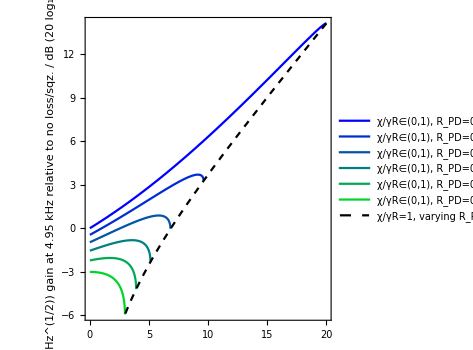
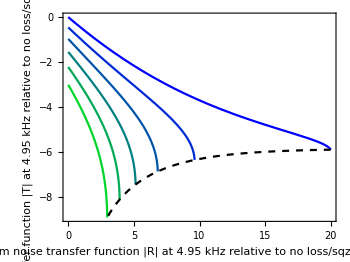

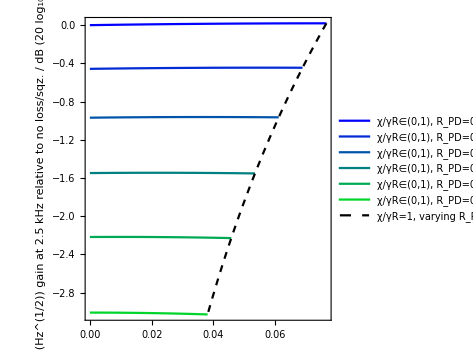
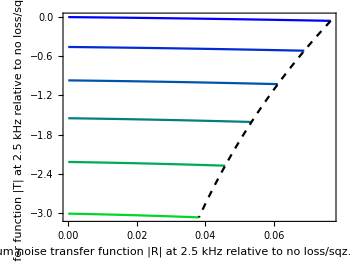

```mathematica
(*fProbe_,pastThreshold_:False,ρRPTrue_:True*)
plotThresholdFinder[0.99 ωs/(2π)(*Hz*)]
plotThresholdFinder[2500(*Hz*)]
(*LIGO Voyager parameters have short linewidth (γR) around ωs*)
```

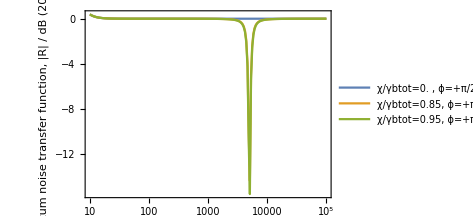
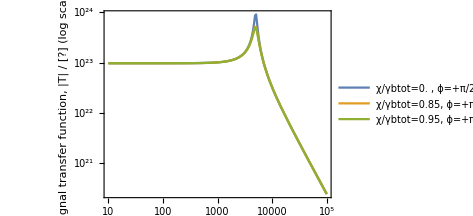
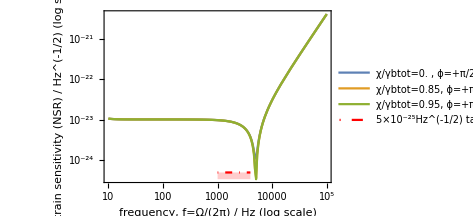

```mathematica
plotwRP[{
{0,π/2,0,0,0},
{0.85γR,π/2,0,0,0},
{0.95γR,π/2,0,0,0}},None,{},10,10^5]
```

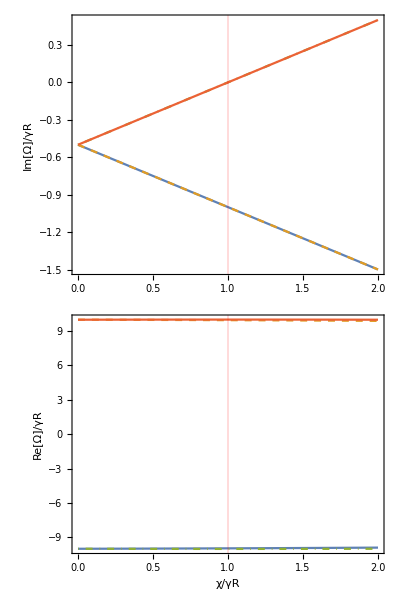

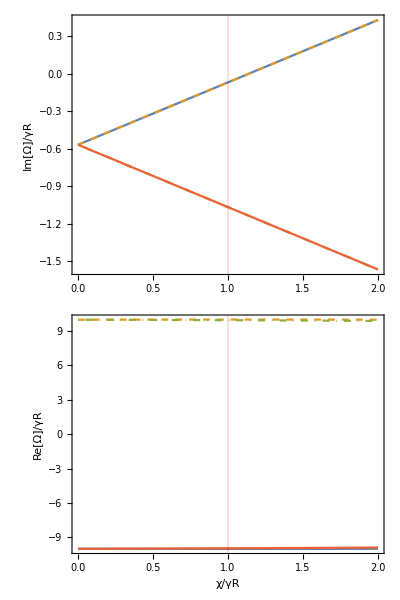

```mathematica
(*plotting stability*)
denom1[Tla_,Tlb_]:=γbtotFn[Tlb]+χ-I Ω+ωs^2/(γaFn[Tla]-ⅈ Ω);
denom2[Tla_,Tlb_]:=(γbtotFn[Tlb]+χ-I Ω+ωs^2/(γaFn[Tla]-ⅈ Ω))((γbtotFn[Tlb]+χ-I Ω+ωs^2/(γaFn[Tla]-ⅈ Ω))/.χ->-χ);
Clear[stabilitydISwRP]
stabilitydISwRP[Tla_,Tlb_]:=(
(*
sol=NSolve[denom1[Tla,Tlb]==0,Ω];
p1=Plot[Evaluate[Table[(Im[Ω/.sol[[i]]]/.{χ->ratio γR})/γR,{i,1,Length[sol]}]],{ratio,0,2},PlotStyle->{,Dashed,DotDashed},
ImagePadding->{{50,2},{1,All}},ImageSize->300,Frame->True,FrameLabel->{{"Im[Ω]/γR",},{,"poles of transfer function\nunstable when Im[Ω]≥0"}},GridLines->{{{1,Red}},None},PerformanceGoal->"Speed"];
p2=Plot[Evaluate[Table[(Re[Ω/.sol[[i]]]/.{χ->ratio γR})/γR,{i,1,Length[sol]}]],{ratio,0,2},PlotStyle->{,Dashed,DotDashed},
ImagePadding->{{50,2},{All,1}},ImageSize->300,Frame->True,FrameLabel->{{"Re[Ω]/γR",},{"χ/γR",}},GridLines->{{{1,Red}},None},PerformanceGoal->"Speed"];
*)
sol=NSolve[denom2[Tla,Tlb]==0,Ω];
p12=Plot[Evaluate[Table[(Im[Ω/.sol[[i]]]/.{χ->ratio γR})/γR,{i,1,Length[sol]}]],{ratio,0,2},PlotStyle->{,Dashed,DotDashed},
ImagePadding->{{50,2},{1,All}},ImageSize->300,Frame->True,FrameLabel->{{"Im[Ω]/γR",},{,StringForm["poles of transfer function\nunstable when Im[Ω]≥0\nT_(l, a)=``, T_(l, b)=``",Tla,Tlb]}},GridLines->{{{1,Red}},None},PerformanceGoal->"Speed"];
p22=Plot[Evaluate[Table[(Re[Ω/.sol[[i]]]/.{χ->ratio γR})/γR,{i,1,Length[sol]}]],{ratio,0,2},PlotStyle->{,Dashed,DotDashed},
ImagePadding->{{50,2},{All,1}},ImageSize->300,Frame->True,FrameLabel->{{"Re[Ω]/γR",},{"χ/γR",}},GridLines->{{{1,Red}},None},PerformanceGoal->"Speed"];
(*Row[{Column[{p1,p2}],Column[{p12,p22}]}]*)
Column[{p12,p22}])

stabilitydISwRP[0,0]
stabilitydISwRP[0.005,0.005]
(*Manipulate[stabilitydISwRP[Tla,Tlb],{Tla,0,1},{Tlb,0,1}]*)
```

value of anti-sqz.'d S_X^(1/2) at sing. threshold value, 20log10: 318.713

'' with RP turned on: 318.713

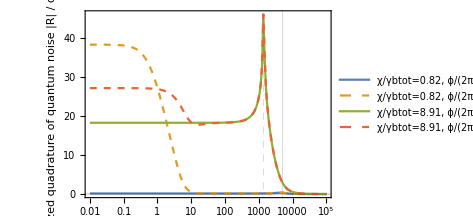
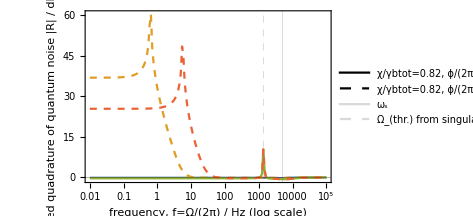

```mathematica
(*plotting both quadratures to verify the effect of the pump phase, and that they are behaving as claimed*)
advancePhaseByPi[params_]:=Insert[Delete[params,2],params[[2]]+π,2]
Clear[plotQNBothQuads]
plotQNBothQuads[valsList_,plotLabel_:None,plotStyle_:{},fRange_:{100(*Hz*),10^5(*Hz*)}]:=(
p1=LogLinearPlot[Evaluate[Table[20Log10[QNwRP@@Join[{2π f},advancePhaseByPi[valsList[[i]]]]],{i,1,Length[valsList]}]],
{f,fRange[[1]],fRange[[2]]},ImageSize->350,
PlotLegends->LineLegend[Table[legendStyler[advancePhaseByPi[valsList[[i]]]],{i,1,Length[valsList]}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],
ImagePadding->{{100,15},{1,All}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{fRange[[1]],fRange[[2]]},All},PlotStyle->plotStyle,Frame->True,FrameLabel->{{"anti-squeezed quadrature\nof quantum noise\n|R| / dB (20log10)",},{,If[ToString[plotLabel]==ToString[None],"degenerate internal squeezing\nparameters of LIGO Voyager\nboth quadratures of quantum noise to verify\ndifference in maximising antisqz. and minimising sqz.",plotLabel]}},
PerformanceGoal->"Speed",GridLines->{{ωs/(2π),{1/(2π)(ωs^2-γaFn[valsList[[-1,3]]]^2)^(1/2),Dashed}},{{0,Directive[Black,Thin]}}}];
p2=LogLinearPlot[Evaluate[Table[20Log10[QNwRP@@Join[{2π f},valsList[[i]]]],{i,1,Length[valsList]}]],
{f,fRange[[1]],fRange[[2]]},ImageSize->350,
PlotLegends->
Labeled[LineLegend[If[plotStyle==={},Table[ColorData[97,i],{i,1,Length[valsList]+1}],plotStyle],Table[legendStyler[valsList[[i]]],{i,1,Length[valsList]}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],LineLegend[{Directive[LightGray,Thick],Directive[LightGray,Dashed]},{"ω_s","Ω_(thr.) from singularity def\nfor last set of parameters"},LabelStyle->10,LegendLabel->"vertical gridlines"]],
ImagePadding->{{100,15},{All,1}},PlotRange->{{fRange[[1]],fRange[[2]]},All},PlotStyle->plotStyle,Frame->True,FrameLabel->{{"squeezed quadrature\nof quantum noise\n|R| / dB (20log10)",},{"frequency, f=Ω/(2π) / Hz (log scale)",}},
PerformanceGoal->"Speed",GridLines->{{ωs/(2π),{1/(2π)(ωs^2-γaFn[valsList[[-1,3]]]^2)^(1/2),Dashed}},{{0,Directive[Black,Thin]}}}];
Column[{p1,p2},Spacings->0])

Block[{pumpPhase0=(1/2+0.01)π,Tla0=0.8,γa=γaFn[Tla0],Tlb0=0.01,γbtot=γbtotFn[Tlb0],Rpd0=0.01},
Print["value of anti-sqz.'d S_X^(1/2) at sing. threshold value, 20log10: ",20 Log10[QNwRP[(ωs^2-γa^2)^(1/2),-(γa+γbtot),π/2,Tla0,Tlb0,Rpd0,False]]]
(*doesn't evaluate to 1/0 because of numerical errors somewhere, I suspect*);Print["'' with RP turned on: ",20 Log10[QNwRP[(ωs^2-γa^2)^(1/2),-(γa+γbtot),π/2,Tla0,Tlb0,Rpd0,True]]];
plotQNBothQuads[{
{γR,pumpPhase0,Tla0,Tlb0,Rpd0,False},
{γR,pumpPhase0,Tla0,Tlb0,Rpd0,True},
{γbtot+γa,pumpPhase0,Tla0,Tlb0,Rpd0,False},
{γbtot+γa,pumpPhase0,Tla0,Tlb0,Rpd0,True}},None,{,Dashed},{10^-2,10^5}]]
(*can change pumpPhase0 to mix the quadratures together*)
```

value of anti-sqz.'d S_X^(1/2) at sing. threshold value, 20log10: 318.713

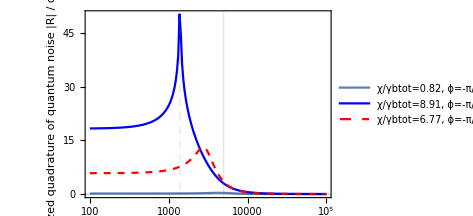
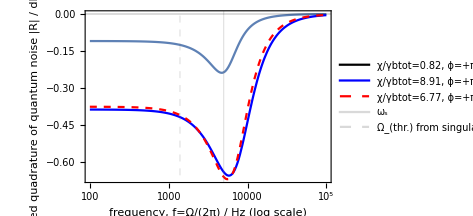

```mathematica
(*watch out when copying from dIS_threshold.nb, QNwRP is Sx^(1/2) compared to Sx1 which is Sx, factor of 2 difference in log*)
Clear[plotQNBothQuadswMin]
plotQNBothQuadswMin[valsList_,plotLabel_:None,plotStyle_:{},fRange_:{100(*Hz*),10^5(*Hz*)}]:=
Block[{γa=γaFn[valsList[[-1,3]]],γbtot=γbtotFn[valsList[[-1,4]]],Rpd=valsList[[-1,5]]},
p1=LogLinearPlot[Evaluate[Join[
Table[20Log10[QNwRP@@Join[{2π f},advancePhaseByPi[valsList[[i]]]]],{i,1,Length[valsList]}],
{20Log10[QNwRP@@Join[{2π f,χSqzMinThresh[γa,γbtot,Rpd]},advancePhaseByPi[valsList[[-1]]][[2;;]]]]}]],
{f,fRange[[1]],fRange[[2]]},ImageSize->350,
PlotLegends->LineLegend[Join[Table[legendStyler[advancePhaseByPi[valsList[[i]]]],{i,1,Length[valsList]}],{legendStyler[Join[{χSqzMinThresh[γa,γbtot,Rpd]},advancePhaseByPi[valsList[[-1]]][[2;;]]]]}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],
ImagePadding->{{100,15},{1,All}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{fRange[[1]],fRange[[2]]},All},PlotStyle->plotStyle,Frame->True,FrameLabel->{{"anti-squeezed quadrature\nof quantum noise\n|R| / dB (20log10)",},{,If[ToString[plotLabel]==ToString[None],"degenerate internal squeezing\nparameters of LIGO Voyager\nboth quadratures of quantum noise to verify\ndifference in maximising antisqz. and minimising sqz.\nlast line is sqz. minimiser",plotLabel]}},
PerformanceGoal->"Speed",GridLines->{{ωs/(2π),{1/(2π)(ωs^2-γaFn[valsList[[-1,3]]]^2)^(1/2),Dashed}},{{0,Directive[Black,Thin]}}}];
p2=LogLinearPlot[Evaluate[Join[
Table[20Log10[QNwRP@@Join[{2π f},valsList[[i]]]],{i,1,Length[valsList]}],
{20 Log10[QNwRP@@Join[{2π f,χSqzMinThresh[γa,γbtot,Rpd]},valsList[[-1]][[2;;]]]]}]],
{f,fRange[[1]],fRange[[2]]},ImageSize->350,
PlotLegends->
Labeled[LineLegend[If[plotStyle=={},Table[ColorData[97,i],{i,1,Length[valsList]+1}],plotStyle],Join[Table[legendStyler[valsList[[i]]],{i,1,Length[valsList]}],{legendStyler[Join[{χSqzMinThresh[γa,γbtot,Rpd]},valsList[[-1]][[2;;]]]]}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],LineLegend[{Directive[LightGray,Thick],Directive[LightGray,Dashed]},{"ω_s","Ω_(thr.) from singularity def\nfor last set of parameters"},LabelStyle->10,LegendLabel->"vertical gridlines"]],
ImagePadding->{{100,15},{All,1}},PlotRange->{{fRange[[1]],fRange[[2]]},All},PlotStyle->plotStyle,Frame->True,FrameLabel->{{"squeezed quadrature\nof quantum noise\n|R| / dB (20log10)",},{"frequency, f=Ω/(2π) / Hz (log scale)",}},
PerformanceGoal->"Speed",GridLines->{{ωs/(2π),{1/(2π)(ωs^2-γaFn[valsList[[-1,3]]]^2)^(1/2),Dashed}},{{0,Directive[Black,Thin]}}}];
Column[{p1,p2},Spacings->0]]

(*seems to be the same for ϵ0 or 0.01 for Tlb and Rpd*)
Block[{pumpPhase0=(1/2+0.00)π,Tla0=0.8,γa=γaFn[Tla0],Tlb0=0.01,γbtot=γbtotFn[Tlb0],Rpd0=0.01},
Print["value of anti-sqz.'d S_X^(1/2) at sing. threshold value, 20log10: ",20 Log10[QNwRP[(ωs^2-γa^2)^(1/2),-(γa+γbtot),π/2,Tla0,Tlb0,Rpd0,False]]]
(*doesn't evaluate to 1/0 because of numerical errors somewhere, I suspect*);
plotQNBothQuadswMin[{
{γR,pumpPhase0,Tla0,Tlb0,Rpd0,False},
{γbtot+γa,pumpPhase0,Tla0,Tlb0,Rpd0,False}},None,{{Grey,Thickness[Small]},Blue,{Red,Dashed}}]]
```

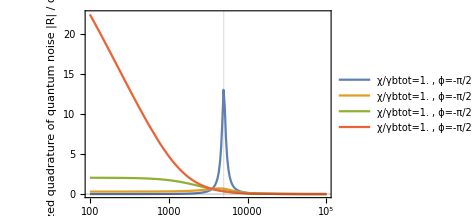
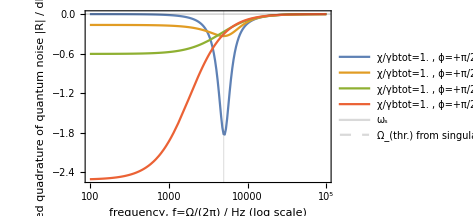

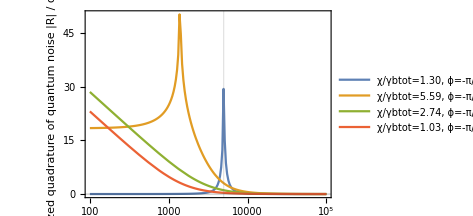
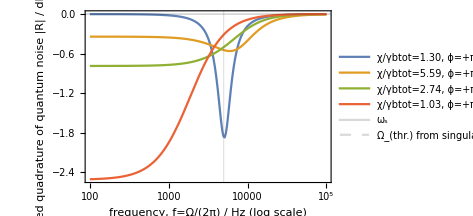

```mathematica
(*transition to dOPO at threshold, both quadratures*)
ϵ0=1 10^-100;
armLossList={0.1,0.8,0.99,1-ϵ0};
Block[{pumpPhase0=(1/2)π,Tlb0=0.05,γbtot=γbtotFn[Tlb0],Rpd0=0.05},
plotQNBothQuads[Flatten[Table[{
{γbtot,pumpPhase0,armLossList[[j]],Tlb0,Rpd0,False}},{j,1,Length[armLossList]}],1]]]
(*now staying at threshold*)
poleSol0={{χ->γbtot+γa},{χ->γbtot+ωs^2/γa}};
χPoleThresh[γa0_,γbtot0_]:=If[γa0≠0,Min[(χ/.poleSol0/.{γa->γa0,γbtot->γbtot0})],χ/.poleSol0[[2]]/.{γa->γa0,γbtot->γbtot0}]
Block[{pumpPhase0=(1/2)π,Tlb0=0.05,γbtot=γbtotFn[Tlb0],Rpd0=0.05},
plotQNBothQuads[Flatten[Table[{
{χPoleThresh[γaFn[armLossList[[j]]],γbtot],pumpPhase0,armLossList[[j]],Tlb0,Rpd0,False}},{j,1,Length[armLossList]}],1]]]
```

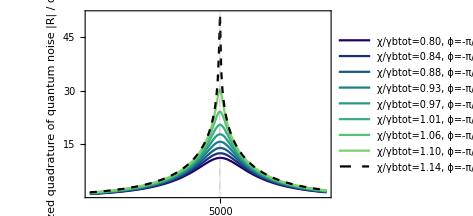
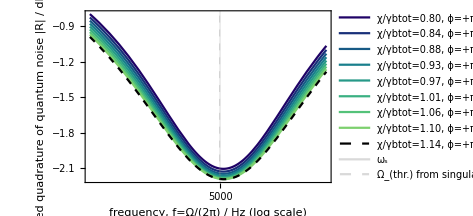

```mathematica
(*consider whether singularity threshold curve creates any kind of envelope for the other curves*)
Block[{pumpPhase0=π/2,Tla0=0.05,Tlb0=0.05,γbtot=γbtotFn[Tlb0],Rpd0=0.05},
χThr=χPoleThresh[γaFn[Tla0],γbtot];
(*Print[χSqzMinThresh[γaFn[Tla0],γbtot,Rpd0]/χThr];*)
χRatioList=Subdivide[0.7,1,8];
plotQNBothQuads[Table[
{χRatioList[[j]]χThr,pumpPhase0,Tla0,Tlb0,Rpd0,False},{j,1,Length[χRatioList]}],None,Join[Table[Blend["BlueGreenYellow",(j-1)/Length[χRatioList]],{j,1,Length[χRatioList]-1}],{Directive[Black,Dashed]}],{4 10^3,6 10^3}]]
(*doesn't look like there's any enveloping*)
```

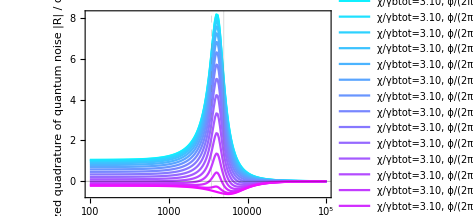
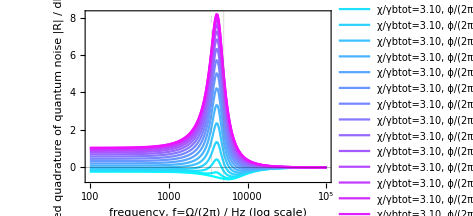

```mathematica
(*plot dIS for different pump phases --> show smooth transition (and don't use sing. threshold)*)
Block[{pumpPhase0=π/2,Tla=0.7,Tlb0=0.05,γbtot=γbtotFn[Tlb0],Rpd0=0.05},
χThr=χPoleThresh[γaFn[Tla],γbtot];
χRatio0=0.7;
phaseList=Subdivide[π/2,3 π/2,16];
plotQNBothQuads[Table[
{χRatio0 χThr,phaseList[[j]],Tla,Tlb0,Rpd0,False},{j,1,Length[phaseList]}],None,Table[Blend[{Cyan,Magenta},(i-1)/Length[phaseList]],{i,1,Length[phaseList]}]]]
```